# Holo Calc13

Anlehnend an “Calc12/Symmetrie und Polstellen.nb” wird hier nochmal die Residuensatz-Loesung fuer A fuer das Holographie-Modell mit n Extradimensionen diskutiert. Dabei suche ich jetzt nach einer geschlossenen Lösung und vertraue der dann.

## 0. Was ist in dieser Rechnung neu?

1. Mitgenommener Faktor 1/r^{n+2}, siehe Seite 2 von Calc12 (kein Effekt auf Polstellen, aber auf Residuenwert)
2. Mitgenommener Faktor (-1)^n, siehe handschriftliche Anmerkungen zu Calc12, Seite 10f

```mathematica
holo[z_,n_] = z^(2+n) / (z^(2+n) + 1);
hD[z_,n_] = D[holo[z,n], z] // Together
(* Eigentliches V was 3+n-dim Fouriertrafo sieht *)
bigV[z_,n_] = 1/z^(2+n) *hD[z,n]
hDzPlus[z_,n_] = z^(1+n) * bigV[z, n] // Together
hDzMinus[z_,n_] =  (-1)^n * z^(1+n)  * bigV[(-z),n] // Together
```

((2+n) z^(1+n))/((1+z^(2+n))^2)

(2+n)/(z (1+z^(2+n))^2)

((2+n) z^n)/((1+z^(2+n))^2)

-((-1)^n (2+n) z^n)/((1+(-z)^n z^2)^2)

### 0.1. Wie sehen diese Funktionen aus?

```mathematica
myPlot[fun_] := Plot[Table[fun[z,n],{n,0,6}]//Evaluate,
{z,-2,2}, 
PlotStyle->(Riffle[#,{Dashed,#}&/@Reverse[#]]& [ColorData[9,"ColorList"]]),
PlotLabel -> "Even and uneven functions "<>ToString[fun],
PlotLegends-> LineLegend[Table[n,{n,0,6}],LegendLabel-> "n="],
ImageSize-> Medium
]
```

-((-1)^n (2+n) z^n HeavisideTheta[-z])/((1+(-z)^n z^2)^2)+((2+n) z^n HeavisideTheta[z])/((1+z^(2+n))^2)

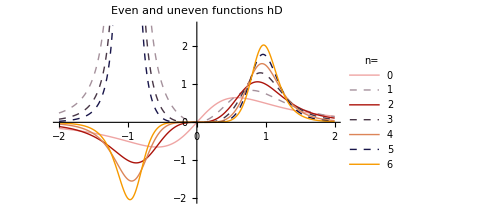
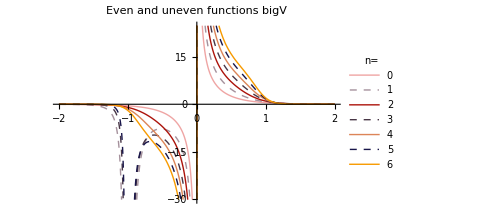
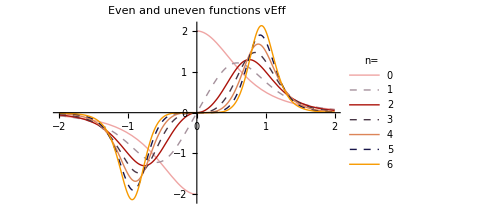

```mathematica
(* Effektives v was 1-dim Fouriertrafo sieht. Diese beiden Formulierungen sind identisch!!  *)
vEff[z_,n_] = z^(1+n)(bigV[z,n]*HeavisideTheta[z] + (-1)^n  bigV[-z,n]*HeavisideTheta[-z]);
vEff[z_,n_] = hDzPlus[z,n]*HeavisideTheta[z] + hDzMinus[z,n]*HeavisideTheta[-z]
myPlot@#&/@{hD,bigV,vEff}
```

Oh je: Bei n=0 sind nicht mal links- und rechtsseitige Werte für z→0 die gleichen! Das bedeutet, dass unser ganzer Ansatz hier ziemlicher Humbug ist.

## 1. Polstellen extrahieren (Rekapituliert)

Nutze Reduce, da besser. Code kopiert aus “Symmetrie für Bardeen.nb”. Das hier ist lediglich ein Mix aus “Symmetrie für Bardeen” (Reduce) und “Symmetrie für Holo”. Nichts neues.

```mathematica
ReduceToSolutions[reduceResult_, extractVariable_] := Cases[reduceResult,Equal[extractVariable, value_]-> value, 100]
```

```mathematica
polReduce[n_, hDzSide_] := Reduce[Denominator@hDzSide[z,n]==0,z]
polstellen[n_,hDzSide_] := polReduce[n,hDzSide]~ ReduceToSolutions ~ z
poles[n_] := Join@@(polstellen[n,#[[1]]]~Select~#[[2]] &)/@{
hDzPlus-> (Im[#]≤ 0 ∧Re[#] ≥ 0&),
 hDzMinus-> (Im[#] ≤ 0 ∧ Re[#] ≤ 0&)
}
```

Pole mit der Hand “nachbauen”. Dazu verstehen wir die bei polReduce gelöste Gleichung mit der Hand nochmal, also (-1) = z^(2+n) hat die Lösungen exp^(2πi (1/2 + k)/(2+n)), k∈Ν.
Um aber nur die Lösungen mit Re>0∧Im<0 zu bekommen, übersetzen wir diese Bedingung in die Winkel: e^(iϕ)=cos(ϕ)+i sin(ϕ) und damit cos(ϕ)>0∧sin(ϕ)<0  ↔  3/2π ≤ ϕ ≤ 2π. Nun ist ϕ=2πi(1/2 + k)/(2+n) und dies erklärt kmin und kmax (Gleichung umgestellt nach k).

```mathematica
(* Mit der Hand "nachgebaute" Pole *)
kmin[n_] = Ceiling[ 1+3/4 n];
kmax[n_] = Floor[ 3/2 + n ];
(* Intervall war: {k,0,2+n}  *)
constructedPoles[n_] :=Table[Exp[2Pi I(1/2 + k) / (2+n)],{k,kmin[n], kmax[n]}]
```

Die an x=0 gespiegelten Pole erhält man trivial durch z_0→ -z_0 in der aufzustellenden Summenformel.

### 1.1. Plot der Polstellen

Das Polstellen-Plotten erfolgt lediglich zur Verifikation. 1:1 genommen von “Symmetrien für Holo”, Check des Plots gegen Calc12 (Seite 9). Passt alles.

```mathematica
(* Zeichne die Polstellen.
Diese Funktion/Zelle ist aus Polstellen.nb kopiert und etwas modifiziert. *)
circle[s_Circle]:=s/.Circle[a_,r_,{start_,end_}]:>({s,Arrow[{#-r/10^2 {-Sin@end,Cos@end},#}]}&[a+r {Cos@end,Sin@end}])
Daten[n_] :={
{Re[#], Im[#]} & /@ (Solve[z^(2+n) == 1,z] /. {{z-> a_}-> a}) , (* in Blau *)
{Re[#], Im[#]} & /@ polstellen[n, hDzPlus],
{Re[#], Im[#]} & /@ polstellen[n, hDzMinus],
{Re[#], Im[#]} & /@ poles[n] (* in Ringen *),
{Re[#], Im[#]} & /@ constructedPoles[n]
}
MakePlot[n_,
label_:"z*h(z) left and right roots vs unit roots. black: Residual taken Points"
] :=Show[ListPlot[
Daten[n],
AxesOrigin-> {0,0},
PlotRange -> {{-1.2,1.2},{-1.2,1.2}},
AspectRatio-> 1,
Frame -> True,
FrameLabel->{{Im,None},{Re,label }},
PlotMarkers -> {
{Graphics[{Blue, Opacity[0.6],Disk[]}], 0.1},
{
Graphics@{Darker@Yellow,
Circle[],
Disk[{0,0},1,{-Pi/2,Pi/2}],
Text[Style["R","Title",15,Bold,Darker@Darker@Brown], {+0.5, Center}]},
 0.1},
{
Graphics@{Lighter@Magenta,
Circle[],
Disk[{0,0},1,{Pi/2,3/2*Pi}],
Text[Style["L","Title",15,Bold,Darker[Magenta]], {-0.5, Center}]},
 0.1},
{Graphics[{Black,Thickness[0.15],Circle[]}],0.12},
{Graphics[{Red,Thickness[0.15],Circle[]}],0.18}
},
PlotRange-> All,
ImageSize->Medium],
Graphics[{Opacity[0.2],Circle[{0,0},1]}],
Graphics@circle[Circle[{0,0},1,{0.1,Pi/(2+n) - 0.1 (* 0.1=our cirlce radius *)}]]
];
Manipulate[Show[
MakePlot[n],
Graphics[{Text[Style[StringForm["n=``",n],{Black, 20}], Offset[{120,130},{0,0}]](*,
Text[Style[StringForm["# Residuen=``",ResidueList[n]//Length],{Black, 20}], Offset[{+30,-30},{0,0}]]*)}
]]
,{n,0,7,1}]
```

Die folgende Tabelle wurde schon oft geschrieben. Hier wird sie nochmal rekapituliert, um einen geschlossenen Ausdruck für die Pole zu entwickeln.

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# unique poles", "# poles","Unique Poles","Constructed Poles"}},
Table[{n,
Length@Union@poles[n],
Length@poles[n],
Union@poles[n] //Arg // N // Sort,
Join[constructedPoles[n], -Conjugate@constructedPoles[n]] // Arg // N // Sort
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # unique poles | # poles | Unique Poles | Constructed Poles
0 | 1 | 2 | {-1.5708} | {-1.5708,-1.5708}
1 | 2 | 2 | {-2.0944,-1.0472} | {-2.0944,-1.0472}
2 | 2 | 2 | {-2.35619,-0.785398} | {-2.35619,-0.785398}
3 | 2 | 2 | {-2.51327,-0.628319} | {-2.51327,-0.628319}
4 | 3 | 4 | {-2.61799,-1.5708,-0.523599} | {-2.61799,-1.5708,-1.5708,-0.523599}
5 | 4 | 4 | {-2.69279,-1.7952,-1.3464,-0.448799} | {-2.69279,-1.7952,-1.3464,-0.448799}
6 | 4 | 4 | {-2.74889,-1.9635,-1.1781,-0.392699} | {-2.74889,-1.9635,-1.1781,-0.392699}
7 | 4 | 4 | {-2.79253,-2.0944,-1.0472,-0.349066} | {-2.79253,-2.0944,-1.0472,-0.349066}

## 2. Berechnung des Holographie-Integrals

```mathematica
IntegralResidueList[n_] := 
(2 Pi I) * (-1)  * Residue[If[Re@# ≥ 0,hDzPlus,hDzMinus][z,n] * Exp[-I p z], {z,#}]& /@ poles[n]
```

```mathematica
IntegralValue[n_] := Total@IntegralResidueList[n]
AValue[p_,n_] :=  I / p * IntegralValue[n]
```

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# poles","Wert für A(p)"}},
Table[{n,
Length@poles[n],
AValue[p,n] ,
AValue[p,n]//ComplexExpand
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # poles | Wert für A(p) | 
0 | 2 | (2 ⅈ ⅇ^-p (1+p) π)/p | ⅈ (2 ⅇ^-p π+(2 ⅇ^-p π)/p)
1 | 2 | (ⅈ (-2/3 ⅇ^((-1)^(5/6) p) ((-1)^(1/6)+p) π-2/3 (-1)^(5/6) ⅇ^(-(-1)^(1/6) p) (1+(-1)^(1/6) p) π))/p | (2 ⅇ^(-(√3 p)/2) π Cos[p/2])/(3 p)+4/3 ⅇ^(-(√3 p)/2) π Sin[p/2]+(2 ⅇ^(-(√3 p)/2) π Sin[p/2])/(√3 p)
2 | 2 | (ⅈ (-1/2 ⅈ ⅇ^(-(-1)^(1/4) p) ((-1)^(1/4)+ⅈ p) π+1/2 ⅈ ⅇ^((-1)^(3/4) p) ((-1)^(3/4)+ⅈ p) π))/p | (ⅇ^(-p/(√2)) π Cos[p/(√2)])/(√2 p)+ⅇ^(-p/(√2)) π Sin[p/(√2)]+(ⅇ^(-p/(√2)) π Sin[p/(√2)])/(√2 p)
3 | 2 | 1/p ⅈ (-2/5 ⅇ^((-1)^(7/10) p) ((-1)^(3/10)+p) π-2/5 (-1)^(7/10) ⅇ^(-(-1)^(3/10) p) (1+(-1)^(3/10) p) π) | (ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (-1-√5) p])/(10 p)+(ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (-1-√5) p])/(2 √5 p)+(ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (1+√5) p])/(10 p)+(ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (1+√5) p])/(2 √5 p)-2/5 ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (-1-√5) p]-(2 √(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (-1-√5) p])/(5 p)+2/5 ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (1+√5) p]+(2 √(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (1+√5) p])/(5 p)+ⅈ (2/5 ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (-1-√5) p]+(2 √(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (-1-√5) p])/(5 p)-2/5 ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (1+√5) p]-(2 √(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (1+√5) p])/(5 p)+(ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (-1-√5) p])/(10 p)+(ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (-1-√5) p])/(2 √5 p)+(ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (1+√5) p])/(10 p)+(ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (1+√5) p])/(2 √5 p))
4 | 4 | 1/p ⅈ (2/3 ⅇ^-p (1+p) π+1/3 (-1)^(5/6) ⅇ^((-1)^(2/3) p) (ⅈ+(-1)^(1/6) p) π-1/3 (-1)^(2/3) ⅇ^(-(-1)^(1/3) p) (1+(-1)^(1/3) p) π) | ⅈ ((2 ⅇ^-p π)/3+(2 ⅇ^-p π)/(3 p))+(ⅇ^(-p/2) π Cos[(√3 p)/2])/(√3 p)+2/3 ⅇ^(-p/2) π Sin[(√3 p)/2]+(ⅇ^(-p/2) π Sin[(√3 p)/2])/(3 p)
5 | 4 | 1/p ⅈ (-2/7 ⅇ^((-1)^(13/14) p) ((-1)^(1/14)+p) π-2/7 ⅇ^((-1)^(9/14) p) ((-1)^(5/14)+p) π-2/7 (-1)^(13/14) ⅇ^(-(-1)^(1/14) p) (1+(-1)^(1/14) p) π-2/7 (-1)^(9/14) ⅇ^(-(-1)^(5/14) p) (1+(-1)^(5/14) p) π) | (4 ⅇ^(-p Sin[π/7]) π Cos[π/7] Cos[p Cos[π/7]])/(7 p)+(4 ⅇ^(-p Cos[π/14]) π Cos[p Sin[π/14]] Sin[π/14])/(7 p)+ⅈ (-2/7 ⅇ^(-p Sin[π/7]) π Cos[p Cos[π/7]]+2/7 ⅇ^(-p Sin[π/7]) π Cos[π/7]^2 Cos[p Cos[π/7]]-2/7 ⅇ^(-p Cos[π/14]) π Cos[p Sin[π/14]]+2/7 ⅇ^(-p Cos[π/14]) π Cos[π/14]^2 Cos[p Sin[π/14]]+2/7 ⅇ^(-p Cos[π/14]) π Cos[p Sin[π/14]] Sin[π/14]^2+2/7 ⅇ^(-p Sin[π/7]) π Cos[p Cos[π/7]] Sin[π/7]^2)+2/7 ⅇ^(-p Sin[π/7]) π Sin[p Cos[π/7]]+2/7 ⅇ^(-p Sin[π/7]) π Cos[π/7]^2 Sin[p Cos[π/7]]+(4 ⅇ^(-p Sin[π/7]) π Sin[π/7] Sin[p Cos[π/7]])/(7 p)+2/7 ⅇ^(-p Sin[π/7]) π Sin[π/7]^2 Sin[p Cos[π/7]]+2/7 ⅇ^(-p Cos[π/14]) π Sin[p Sin[π/14]]+(4 ⅇ^(-p Cos[π/14]) π Cos[π/14] Sin[p Sin[π/14]])/(7 p)+2/7 ⅇ^(-p Cos[π/14]) π Cos[π/14]^2 Sin[p Sin[π/14]]+2/7 ⅇ^(-p Cos[π/14]) π Sin[π/14]^2 Sin[p Sin[π/14]]
6 | 4 | 1/p ⅈ (-1/4 ⅇ^((-1)^(7/8) p) ((-1)^(1/8)+p) π-1/4 ⅇ^((-1)^(5/8) p) ((-1)^(3/8)+p) π-1/4 (-1)^(7/8) ⅇ^(-(-1)^(1/8) p) (1+(-1)^(1/8) p) π-1/4 (-1)^(5/8) ⅇ^(-(-1)^(3/8) p) (1+(-1)^(3/8) p) π) | (ⅇ^(-p Sin[π/8]) π Cos[π/8] Cos[p Cos[π/8]])/(2 p)+(ⅇ^(-p Cos[π/8]) π Cos[p Sin[π/8]] Sin[π/8])/(2 p)+ⅈ (-1/4 ⅇ^(-p Sin[π/8]) π Cos[p Cos[π/8]]+1/4 ⅇ^(-p Sin[π/8]) π Cos[π/8]^2 Cos[p Cos[π/8]]-1/4 ⅇ^(-p Cos[π/8]) π Cos[p Sin[π/8]]+1/4 ⅇ^(-p Cos[π/8]) π Cos[π/8]^2 Cos[p Sin[π/8]]+1/4 ⅇ^(-p Sin[π/8]) π Cos[p Cos[π/8]] Sin[π/8]^2+1/4 ⅇ^(-p Cos[π/8]) π Cos[p Sin[π/8]] Sin[π/8]^2)+1/4 ⅇ^(-p Sin[π/8]) π Sin[p Cos[π/8]]+1/4 ⅇ^(-p Sin[π/8]) π Cos[π/8]^2 Sin[p Cos[π/8]]+(ⅇ^(-p Sin[π/8]) π Sin[π/8] Sin[p Cos[π/8]])/(2 p)+1/4 ⅇ^(-p Sin[π/8]) π Sin[π/8]^2 Sin[p Cos[π/8]]+1/4 ⅇ^(-p Cos[π/8]) π Sin[p Sin[π/8]]+(ⅇ^(-p Cos[π/8]) π Cos[π/8] Sin[p Sin[π/8]])/(2 p)+1/4 ⅇ^(-p Cos[π/8]) π Cos[π/8]^2 Sin[p Sin[π/8]]+1/4 ⅇ^(-p Cos[π/8]) π Sin[π/8]^2 Sin[p Sin[π/8]]
7 | 4 | 1/p ⅈ (-2/9 ⅇ^((-1)^(5/6) p) ((-1)^(1/6)+p) π-2/9 ⅇ^((-1)^(11/18) p) ((-1)^(7/18)+p) π-2/9 (-1)^(5/6) ⅇ^(-(-1)^(1/6) p) (1+(-1)^(1/6) p) π-2/9 (-1)^(11/18) ⅇ^(-(-1)^(7/18) p) (1+(-1)^(7/18) p) π) | (2 ⅇ^(-(√3 p)/2) π Cos[p/2])/(9 p)+(4 ⅇ^(-p Sin[π/9]) π Cos[π/9] Cos[p Cos[π/9]])/(9 p)+4/9 ⅇ^(-(√3 p)/2) π Sin[p/2]+(2 ⅇ^(-(√3 p)/2) π Sin[p/2])/(3 √3 p)+ⅈ (-2/9 ⅇ^(-p Sin[π/9]) π Cos[p Cos[π/9]]+2/9 ⅇ^(-p Sin[π/9]) π Cos[π/9]^2 Cos[p Cos[π/9]]+2/9 ⅇ^(-p Sin[π/9]) π Cos[p Cos[π/9]] Sin[π/9]^2)+2/9 ⅇ^(-p Sin[π/9]) π Sin[p Cos[π/9]]+2/9 ⅇ^(-p Sin[π/9]) π Cos[π/9]^2 Sin[p Cos[π/9]]+(4 ⅇ^(-p Sin[π/9]) π Sin[π/9] Sin[p Cos[π/9]])/(9 p)+2/9 ⅇ^(-p Sin[π/9]) π Sin[π/9]^2 Sin[p Cos[π/9]]

```mathematica
Grid[({{"n", "# poles", "Wert für A(p)", Null}, {0, 2, (2 ⅈ (p+1) π)/(ⅇ^p p), (2 ⅈ (p+1) π)/(ⅇ^p p)}, {1, 2, (ⅈ (-(2 (-1)^(5/6) (-1^(1/6) p+1) π)/(3 ⅇ^(-1^(1/6) p))-2/3 (p+-1^(1/6)) ⅇ^((-1)^(5/6) p) π))/p, (2 π (cos(p/2)+sin(p/2) (2 p+√3)))/(ⅇ^((√3 p)/2) (3 p))}, {2, 2, (ⅈ (1/2 ⅈ ⅇ^((-1)^(3/4) p) (ⅈ p+(-1)^(3/4)) π-(ⅈ (ⅈ p+-1^(1/4)) π)/(2 ⅇ^(-1^(1/4) p))))/p, (π (cos(p/(√2)) √2+sin(p/(√2)) (2 p+√2)))/(ⅇ^(p/(√2)) (2 p))}, {3, 2, (ⅈ (-(2 (-1)^(7/10) ((-1)^(3/10) p+1) π)/(5 ⅇ^((-1)^(3/10) p))-2/5 (p+(-1)^(3/10)) ⅇ^((-1)^(7/10) p) π))/p, (ⅇ^(p Root[16 #1^4-20 #1^2+5&,2]) π (cos(1/4 (√5+1) p) (√5+1)+sin(1/4 (√5+1) p) (4 p+√(10-2 √5))))/(5 p)}, {4, 4, (ⅈ ((2 π (p+1))/(3 ⅇ^p)-((-1)^(2/3) (-1^(1/3) p+1) π)/(3 ⅇ^(-1^(1/3) p))+1/3 (-1)^(5/6) ⅇ^((-1)^(2/3) p) (ⅈ+-1^(1/6) p) π))/p, (π (2 ⅈ (p+1)+ⅇ^(p/2) ((2 p+1) sin((√3 p)/2)+cos((√3 p)/2) √3)))/(ⅇ^p (3 p))}, {5, 4, (ⅈ (-(2 (-1)^(13/14) (-1^(1/14) p+1) π)/(7 ⅇ^(-1^(1/14) p))-(2 (-1)^(9/14) ((-1)^(5/14) p+1) π)/(7 ⅇ^((-1)^(5/14) p))-2/7 (p+-1^(1/14)) ⅇ^((-1)^(13/14) p) π-2/7 ⅇ^((-1)^(9/14) p) (p+(-1)^(5/14)) π))/p, (4 π ((cos(1/7 (π-7 p cos(π/7)))+p sin(p cos(π/7))) (cosh(p cos(π/14))+sinh(p cos(π/14)))+(sin(p sin(π/14)+π/14)+p sin(p sin(π/14))) (cosh(p sin(π/7))+sinh(p sin(π/7)))))/((7 p) ⅇ^(p (cos(π/14)+sin(π/7))))}, {6, 4, (ⅈ (-((-1)^(7/8) (-1^(1/8) p+1) π)/(4 ⅇ^(-1^(1/8) p))-((-1)^(5/8) ((-1)^(3/8) p+1) π)/(4 ⅇ^((-1)^(3/8) p))-1/4 (p+-1^(1/8)) ⅇ^((-1)^(7/8) p) π-1/4 ⅇ^((-1)^(5/8) p) (p+(-1)^(3/8)) π))/p, (ⅇ^(p sin(π/8)) π (sin(p sin(π/8)+π/8)+p sin(p sin(π/8)))+ⅇ^(p cos(π/8)) π (cos(1/8 (π-8 p cos(π/8)))+p sin(p cos(π/8))))/((2 p) ⅇ^(p (cos(π/8)+sin(π/8))))}, {7, 4, (ⅈ (-(2 (-1)^(5/6) (-1^(1/6) p+1) π)/(9 ⅇ^(-1^(1/6) p))-(2 (-1)^(11/18) ((-1)^(7/18) p+1) π)/(9 ⅇ^((-1)^(7/18) p))-2/9 (p+-1^(1/6)) ⅇ^((-1)^(5/6) p) π-2/9 ⅇ^((-1)^(11/18) p) (p+(-1)^(7/18)) π))/p, (2 π ((cos(p/2)+sin(p/2) (2 p+√3))/ⅇ^((√3 p)/2)+(2 (cos(1/9 (π-9 p cos(π/9)))+p sin(p cos(π/9))))/ⅇ^(p sin(π/9))))/(9 p)}}),Alignment->{Left,Left},Frame->All,ItemSize->{Automatic,Automatic}] v
```

```mathematica
{{(2 ⅇ^(-(√3 p)/2) π (Cos[p/2]+(√3+2 p) Sin[p/2]))/(3 p)}, {(ⅇ^(-p/(√2)) π (√2 Cos[p/(√2)]+(√2+2 p) Sin[p/(√2)]))/(2 p)}, {1/(5 p)ⅇ^(p Root[5-20 #1^2+16 #1^4&,2]) π ((1+√5) Cos[1/4 (1+√5) p]+(√(10-2 √5)+4 p) Sin[1/4 (1+√5) p])}, {(ⅇ^-p π (2 ⅈ (1+p)+ⅇ^(p/2) (√3 Cos[(√3 p)/2]+(1+2 p) Sin[(√3 p)/2])))/(3 p)}, {1/(7 p)4 ⅇ^(-p (Cos[π/14]+Sin[π/7])) π ((Cos[1/7 (π-7 p Cos[π/7])]+p Sin[p Cos[π/7]]) (Cosh[p Cos[π/14]]+Sinh[p Cos[π/14]])+(p Sin[p Sin[π/14]]+Sin[π/14+p Sin[π/14]]) (Cosh[p Sin[π/7]]+Sinh[p Sin[π/7]]))}, {1/(2 p)ⅇ^(-p (Cos[π/8]+Sin[π/8])) (ⅇ^(p Cos[π/8]) π (Cos[1/8 (π-8 p Cos[π/8])]+p Sin[p Cos[π/8]])+ⅇ^(p Sin[π/8]) π (p Sin[p Sin[π/8]]+Sin[π/8+p Sin[π/8]]))}, {1/(9 p)2 π (ⅇ^(-(√3 p)/2) (Cos[p/2]+(√3+2 p) Sin[p/2])+2 ⅇ^(-p Sin[π/9]) (Cos[1/9 (π-9 p Cos[π/9])]+p Sin[p Cos[π/9]]))}}//Flatten
```

{(2 ⅇ^(-(√3 p)/2) π (Cos[p/2]+(√3+2 p) Sin[p/2]))/(3 p),(ⅇ^(-p/(√2)) π (√2 Cos[p/(√2)]+(√2+2 p) Sin[p/(√2)]))/(2 p),(ⅇ^(p Root[5-20 #1^2+16 #1^4&,2]) π ((1+√5) Cos[1/4 (1+√5) p]+(√(10-2 √5)+4 p) Sin[1/4 (1+√5) p]))/(5 p),(ⅇ^-p π (2 ⅈ (1+p)+ⅇ^(p/2) (√3 Cos[(√3 p)/2]+(1+2 p) Sin[(√3 p)/2])))/(3 p),1/(7 p)4 ⅇ^(-p (Cos[π/14]+Sin[π/7])) π ((Cos[1/7 (π-7 p Cos[π/7])]+p Sin[p Cos[π/7]]) (Cosh[p Cos[π/14]]+Sinh[p Cos[π/14]])+(p Sin[p Sin[π/14]]+Sin[π/14+p Sin[π/14]]) (Cosh[p Sin[π/7]]+Sinh[p Sin[π/7]])),1/(2 p)ⅇ^(-p (Cos[π/8]+Sin[π/8])) (ⅇ^(p Cos[π/8]) π (Cos[1/8 (π-8 p Cos[π/8])]+p Sin[p Cos[π/8]])+ⅇ^(p Sin[π/8]) π (p Sin[p Sin[π/8]]+Sin[π/8+p Sin[π/8]])),(2 π (ⅇ^(-(√3 p)/2) (Cos[p/2]+(√3+2 p) Sin[p/2])+2 ⅇ^(-p Sin[π/9]) (Cos[1/9 (π-9 p Cos[π/9])]+p Sin[p Cos[π/9]])))/(9 p)}

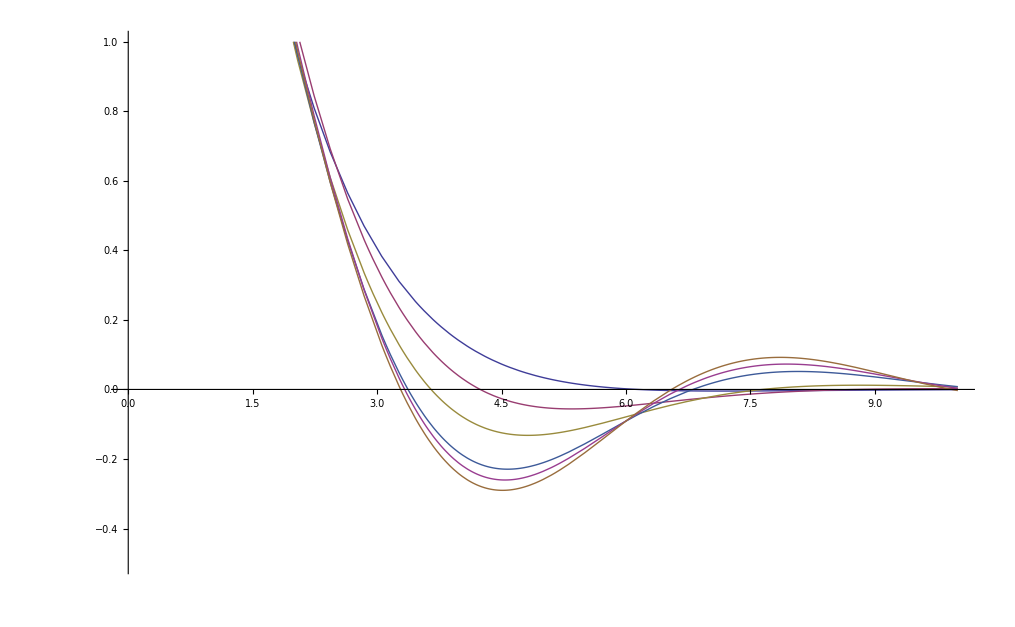

```mathematica
Plot[{(2 ⅇ^(-(√3 p)/2) π (Cos[p/2]+(√3+2 p) Sin[p/2]))/(3 p),(ⅇ^(-p/(√2)) π (√2 Cos[p/(√2)]+(√2+2 p) Sin[p/(√2)]))/(2 p),(ⅇ^(p Root[5-20 #1^2+16 #1^4&,2]) π ((1+√5) Cos[1/4 (1+√5) p]+(√(10-2 √5)+4 p) Sin[1/4 (1+√5) p]))/(5 p),(ⅇ^-p π (2 ⅈ (1+p)+ⅇ^(p/2) (√3 Cos[(√3 p)/2]+(1+2 p) Sin[(√3 p)/2])))/(3 p),1/(7 p)4 ⅇ^(-p (Cos[π/14]+Sin[π/7])) π ((Cos[1/7 (π-7 p Cos[π/7])]+p Sin[p Cos[π/7]]) (Cosh[p Cos[π/14]]+Sinh[p Cos[π/14]])+(p Sin[p Sin[π/14]]+Sin[π/14+p Sin[π/14]]) (Cosh[p Sin[π/7]]+Sinh[p Sin[π/7]])),1/(2 p)ⅇ^(-p (Cos[π/8]+Sin[π/8])) (ⅇ^(p Cos[π/8]) π (Cos[1/8 (π-8 p Cos[π/8])]+p Sin[p Cos[π/8]])+ⅇ^(p Sin[π/8]) π (p Sin[p Sin[π/8]]+Sin[π/8+p Sin[π/8]])),(2 π (ⅇ^(-(√3 p)/2) (Cos[p/2]+(√3+2 p) Sin[p/2])+2 ⅇ^(-p Sin[π/9]) (Cos[1/9 (π-9 p Cos[π/9])]+p Sin[p Cos[π/9]])))/(9 p)},{p,0,10},PlotRange->{-0.5,1.0}]
```